# Linearized Equation Analysis (Structure Factor)

```mathematica
Quit[]
```

## Basic Settings

```mathematica
(* dimensionless variables: a=alpha, b=beta, C, xi, g=G[xi] *)
(* quantities having units: nb, r, dt, Sk[xi] *)
```

```mathematica
(* diffusion operators: dn/dt=LD*n+KD*Wt *)
LD=-r g xi^2;
KDsq=2 nb r g xi^2;
```

```mathematica
(* reaction operators: dn/dt=LR*n+KR*Wt *)
LR=-r;
KRsq=2nb r C;
```

```mathematica
(* exact solution: n(dt)=M*n(0)+N*Y *)
Mex=Exp[(LD+LR)dt];
Nsqex=-(KDsq+KRsq)(1-Exp[2(LD+LR)dt])/2/(LD+LR);
```

```mathematica
(* true structure factor *)
SkExact[xi_]:=nb(C+xi^2)/(1+xi^2)
```

```mathematica
(* correction factor for spatial descretization *)
G[xi_]:=Sin[Sqrt[a/b]xi/2]^2/(Sqrt[a/b]xi/2)^2
```

```mathematica
(* exact reaction: R=(Exp[-r*tau]-1)n+Sqrt[(1-Exp[-2*r*tau])nb*C]Y *)
R[n_,tau_,Y_]:=(Exp[LR tau]-1)n+Sqrt[-KRsq(1-Exp[2LR tau])/2/LR]Y
```

```mathematica
(* 1st-order reaction: R=-r*tau*n+Sqrt[2*r*tau*nb*C]Y *)
R1[n_,tau_,Y_]:=LR tau n+Sqrt[KRsq tau]Y
```

```mathematica
(* multinomial diffusion *)
Mmn[tau_]:=1+LD tau 
Nmnsq[tau_]:=(1-Mmn[tau]^2)nb
Dmn[n_,tau_,Y_]:=(Mmn[tau]-1)n+Sqrt[Nmnsq[tau]]Y
```

## Calculation of S(k) from Each Second-Order Scheme

### Splitting: CN/2 + SSA + CN/2

```mathematica
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y1,ntmp];
nCN=ntmp/.First[%];
nSSA=nCN+R[nCN,dt,Y2];
Solve[ntmp==nSSA+LD(nSSA/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y3,ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkCN2SSACN2[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((16 nb r^2 xi^2-16 C nb r^2 xi^2+24 nb r^2 xi^4-24 C nb r^2 xi^4+9 nb r^2 xi^6-9 C nb r^2 xi^6) dt^2)/(48 (1+xi^2)^2)+O[dt]^(5/2)

### Splitting: SSA/2 + CN + SSA/2

```mathematica
nSSA=n0+R[n0,dt/2,Y1];
Solve[ntmp==nSSA+LD(nSSA/2+ntmp/2)dt+Sqrt[KDsq dt]Y2,ntmp];
nCN=ntmp/.First[%];
n1=nCN+R[nCN,dt/2,Y3];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkSSA2CNSSA2[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((-2 nb r^2 xi^2+2 C nb r^2 xi^2-6 nb r^2 xi^4+6 C nb r^2 xi^4-3 nb r^2 xi^6+3 C nb r^2 xi^6) dt^2)/(12 (1+xi^2)^2)+O[dt]^(5/2)

### Splitting: CN/2 + 2nd-Order Tau-Leaping + CN/2

```mathematica
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y1,ntmp];
nCN=ntmp/.First[%];
ni=(1+LR dt/2)nCN+Sqrt[KRsq dt/2]Y2;
nTau=nCN+LR dt ni+Sqrt[KRsq dt/2] Y2+Sqrt[KRsq dt/2] Y3;
Solve[ntmp==nTau+LD(nTau/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y4,ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkCN2TauCN2[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((8 nb r^2 xi^2-8 C nb r^2 xi^2+8 nb r^2 xi^4-8 C nb r^2 xi^4+3 nb r^2 xi^6-3 C nb r^2 xi^6) dt^2)/(16 (1+xi^2)^2)+O[dt]^(5/2)

### Splitting: (2nd-Order Tau-Leaping)/2 + CN + (2nd-Order Tau-Leaping)/2

```mathematica
ni=(1+LR dt/4)n0+Sqrt[KRsq dt/4]Y1;
nTau=n0+LR (dt/2) ni+Sqrt[KRsq dt/4] Y1+Sqrt[KRsq dt/4] Y2;
Solve[ntmp==nTau+LD(nTau/2+ntmp/2)dt+Sqrt[KDsq dt]Y3,ntmp];
nCN=ntmp/.First[%];
nii=(1+LR dt/4)nCN+Sqrt[KRsq dt/4]Y4;
n1=nCN+LR (dt/2) nii+Sqrt[KRsq dt/4] Y4+Sqrt[KRsq dt/4] Y5;
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2+Coefficient[n1,Y5]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkTau2CNTau2[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((-nb r^2 xi^2+C nb r^2 xi^2-4 nb r^2 xi^4+4 C nb r^2 xi^4-2 nb r^2 xi^6+2 C nb r^2 xi^6) dt^2)/(8 (1+xi^2)^2)+O[dt]^(5/2)

### Unsplitting: Implicit Midpoint with SSA (Midpoint from Backward Euler)

```mathematica
Solve[ntmp==n0+LD ntmp dt/2+Sqrt[KDsq dt/2] Y1,ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y2+R[ni,dt,Y3],ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkImBEMidSSA[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((2 nb r^2 xi^2-2 C nb r^2 xi^2+3 nb r^2 xi^4-3 C nb r^2 xi^4) dt^2)/(6 (1+xi^2)^2)+O[dt]^(5/2)

### Unsplitting: Implicit Midpoint with SSA (Midpoint from CN)

```mathematica
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt/2+Sqrt[KDsq dt/2] Y1,ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y2+R[ni,dt,Y3],ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkImCNMidSSA[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((8 nb r^2 xi^2-8 C nb r^2 xi^2+6 nb r^2 xi^4-9 C nb r^2 xi^4-3 nb r^2 xi^6) dt^2)/(24 (1+xi^2)^2)+O[dt]^(5/2)

### Unsplitting: Implicit Midpoint with Tau-Leaping (Midpoint from Backward Euler)

```mathematica
Solve[ntmp==n0+LD ntmp dt/2+Sqrt[KDsq dt/2] Y1+R1[n0,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R1[n0,dt/2,Y2]+R1[2ni-n0,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,3}]
SkImBEMidTau[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((C nb r^3+nb r^3 xi^2-C nb r^3 xi^2-nb r^3 xi^4) dt^3)/(8 (1+xi^2))+O[dt]^(7/2)

### Unsplitting: Implicit Midpoint with Tau-Leaping (Midpoint from CN)

```mathematica
Solve[ntmp==n0+LD (n0/2+ntmp/2) dt/2+Sqrt[KDsq dt/2] Y1+R1[n0,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R1[n0,dt/2,Y2]+R1[2ni-n0,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkImCNMidTau[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((-C nb r^2 xi^2-nb r^2 xi^4) dt^2)/(8 (1+xi^2))+O[dt]^(5/2)

### Unsplitting: Explicit Midpoint with SSA

```mathematica
Solve[ntmp==n0+LD n0 dt/2+Sqrt[KDsq dt/2] Y1,ntmp];
nii=ntmp/.First[%];
Solve[ntmp==n0+LD n0 dt/2+Sqrt[KDsq dt/2] Y1+R[nii,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD ni dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R[nii,dt/2,Y2]+R[ni,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkExMidSSA[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((8 nb r^2 xi^2-5 C nb r^2 xi^2+15 nb r^2 xi^4-6 C nb r^2 xi^4+6 nb r^2 xi^6) dt^2)/(24 (1+xi^2)^2)+O[dt]^(5/2)

### Unsplitting: Explicit Midpoint with Tau-Leaping

```mathematica
Solve[ntmp==n0+LD n0 dt/2+Sqrt[KDsq dt/2] Y1+R1[n0,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD ni dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R1[n0,dt/2,Y2]+R1[2ni-n0,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

O[dt]^3

O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,3}]
SkExMidTau[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

1/8 (C nb r^3+nb r^3 xi^2+2 C nb r^3 xi^2+2 nb r^3 xi^4+C nb r^3 xi^4+nb r^3 xi^6) dt^3+O[dt]^(7/2)

### Splitting: Multinomial/2 + SSA + Multinomial/2

```mathematica
nMN=n0+Dmn[n0,dt/2,Y1];
nSSA=nMN+R[nMN,dt,Y2];
n1=nSSA+Dmn[nSSA,dt/2,Y3];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

-1/4 (g^2 r^2 xi^4) dt^2+O[dt]^3

1/2 g^2 nb r^2 xi^4 dt^2+O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkMN2SSAMN2[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((nb r xi^4-C nb r xi^4) dt)/(4 (1+xi^2)^2)+((16 nb r^2 xi^2-16 C nb r^2 xi^2+40 nb r^2 xi^4-40 C nb r^2 xi^4+36 nb r^2 xi^6-36 C nb r^2 xi^6+9 nb r^2 xi^8-9 C nb r^2 xi^8) dt^2)/(48 (1+xi^2)^3)+O[dt]^(5/2)

### Splitting: SSA/2 + Multinomial + SSA/2

```mathematica
nSSA=n0+R[n0,dt/2,Y1];
nMN=nSSA+Dmn[nSSA,dt,Y2];
n1=nMN+R[nMN,dt/2,Y3];
```

```mathematica
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mex,{dt,0,2}]
Series[Nsq-Nsqex,{dt,0,2}]
```

-1/2 (g^2 r^2 xi^4) dt^2+O[dt]^3

g^2 nb r^2 xi^4 dt^2+O[dt]^3

```mathematica
Series[Nsq/(1-M^2)-SkExact[xi]/.g->1,{dt,0,2}]
SkSSA2MNSSA2[xi_]:=Evaluate[Nsq/(1-M^2)/.{dt->a/r,g->G[xi]}]
```

((nb r xi^4-C nb r xi^4) dt)/(2 (1+xi^2)^2)+((-2 nb r^2 xi^2+2 C nb r^2 xi^2-8 nb r^2 xi^4+8 C nb r^2 xi^4-6 nb r^2 xi^6+6 C nb r^2 xi^6-3 nb r^2 xi^8+3 C nb r^2 xi^8) dt^2)/(12 (1+xi^2)^3)+O[dt]^(5/2)

## Comparison with Simulation Result of Schlogl Monomodal

```mathematica
(* Basically, you can change alphaVal and betaVal *)
k10=1.5;k20=0.6;k30=2.05;k40=2.95;nbVal=1.;
r0=-D[k10 n^2-k20 n^3+k30-k40 n,n]/.n->nbVal;
G0=(k10 n^2+k20 n^3+k30+k40 n)/2/.n->nbVal;
dx=1.;dt=1.;alphaVal=0.05;betaVal=0.2;
rm=alphaVal/r0
DFick=betaVal
CVal=G0/nbVal/r0
```

0.0285714

0.2

2.02857

```mathematica
S0[xi_]:=Evaluate[SkExact[xi]/.{nb->nbVal,C->CVal}]
S1[xi_,alpha_,beta_]:=Evaluate[SkCN2SSACN2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S2[xi_,alpha_,beta_]:=Evaluate[SkSSA2CNSSA2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S3[xi_,alpha_,beta_]:=Evaluate[SkCN2TauCN2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S4[xi_,alpha_,beta_]:=Evaluate[SkTau2CNTau2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S5[xi_,alpha_,beta_]:=Evaluate[SkImBEMidSSA[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S6[xi_,alpha_,beta_]:=Evaluate[SkImCNMidSSA[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S7[xi_,alpha_,beta_]:=Evaluate[SkImBEMidTau[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S8[xi_,alpha_,beta_]:=Evaluate[SkImCNMidTau[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S9[xi_,alpha_,beta_]:=Evaluate[SkExMidSSA[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S10[xi_,alpha_,beta_]:=Evaluate[SkExMidTau[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S11[xi_,alpha_,beta_]:=Evaluate[SkMN2SSAMN2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S12[xi_,alpha_,beta_]:=Evaluate[SkSSA2MNSSA2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
```

```mathematica
xiMax[alpha_,beta_]:=Sqrt[beta/alpha]Pi
```

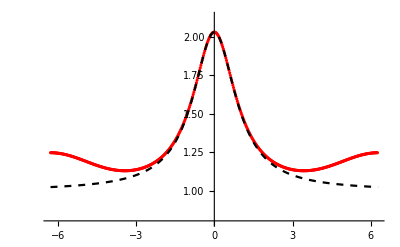

```mathematica
(* Choose a scheme you want to calculate *)
(* Check dt,dx,Ncell *)
Ncell=512;
res=Table[{i xiMax[alphaVal,betaVal]/(Ncell/2),S10[i xiMax[alphaVal,betaVal]/(Ncell/2),alphaVal,betaVal]},{i,-Ncell/2,Ncell/2-1}];
graph1=ListPlot[res,PlotRange->{0.8 nbVal,1.05 nbVal CVal},PlotStyle->Red];
graph2=Plot[SkExact[xi]/.{nb->nbVal,C->CVal},{xi,-xiMax[alphaVal,betaVal],xiMax[alphaVal,betaVal]},PlotStyle->{Black,Dashed}];
Show[{graph1,graph2}]
```

```mathematica
(* file output: xi vs Sk(xi) *)
Export["res.dat",N[res],"Table"]
```

res.dat

## Comparison for Analysis Purpose

```mathematica
(* you can simply set nb and C *)
nbVal=1;CVal=2;
```

```mathematica
S0[xi_]:=Evaluate[SkExact[xi]/.{nb->nbVal,C->CVal}]
S1[xi_,alpha_,beta_]:=Evaluate[SkCN2SSACN2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S2[xi_,alpha_,beta_]:=Evaluate[SkSSA2CNSSA2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S3[xi_,alpha_,beta_]:=Evaluate[SkCN2TauCN2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S4[xi_,alpha_,beta_]:=Evaluate[SkTau2CNTau2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S5[xi_,alpha_,beta_]:=Evaluate[SkImBEMidSSA[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S6[xi_,alpha_,beta_]:=Evaluate[SkImCNMidSSA[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S7[xi_,alpha_,beta_]:=Evaluate[SkImBEMidTau[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S8[xi_,alpha_,beta_]:=Evaluate[SkImCNMidTau[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S9[xi_,alpha_,beta_]:=Evaluate[SkExMidSSA[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S10[xi_,alpha_,beta_]:=Evaluate[SkExMidTau[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S11[xi_,alpha_,beta_]:=Evaluate[SkMN2SSAMN2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
S12[xi_,alpha_,beta_]:=Evaluate[SkSSA2MNSSA2[xi]/.{a->alpha,b->beta,nb->nbVal,C->CVal}]
```

```mathematica
xiMax[alpha_,beta_]:=Sqrt[beta/alpha]Pi
```

### Comparison of Implicit Schemes: Splitting vs. Unsplitting

```mathematica
alpha0=0.1;
Manipulate[Plot[{S1[xi,alpha0,beta],S3[xi,alpha0,beta],S5[xi,alpha0,beta],S7[xi,alpha0,beta],S0[xi]},{xi,-xiMax[alpha0,beta],xiMax[alpha0,beta]},PlotRange->{0.5nbVal,1.25S0[0]},PlotStyle->{Red,{Blue,Dashed},Green,{Purple,Dashed},{Black,Dotted}},PlotLegends->{"CN/2+SSA+CN/2","CN/2+Tau+CN/2","ImMid+SSA(BE-Mid)","ImMid+Tau(BE-Mid)","Exact"}],{beta,1,10}]
```

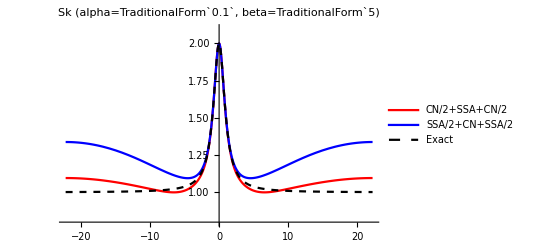

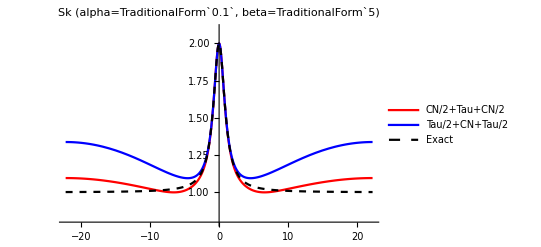

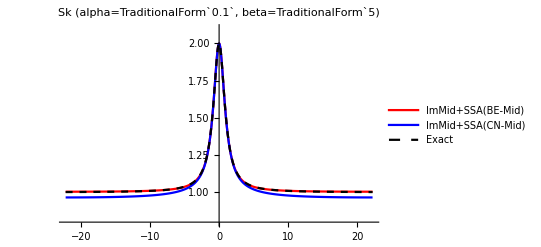

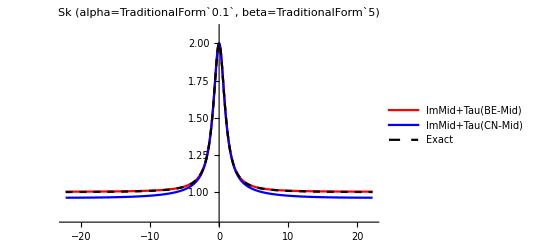

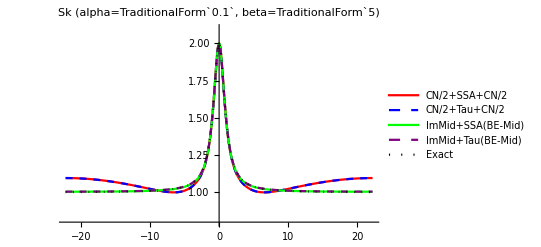

```mathematica
alpha0=0.1;
beta0=5;
Plot[{S1[xi,alpha0,beta0],S2[xi,alpha0,beta0],S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,{Black,Dashed}},PlotLegends->{"CN/2+SSA+CN/2","SSA/2+CN+SSA/2","Exact"},PlotLabel->StringForm["Sk (alpha=``, beta=``)",alpha0,beta0]]
Plot[{S3[xi,alpha0,beta0],S4[xi,alpha0,beta0],S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,{Black,Dashed}},PlotLegends->{"CN/2+Tau+CN/2","Tau/2+CN+Tau/2","Exact"},PlotLabel->StringForm["Sk (alpha=``, beta=``)",alpha0,beta0]]
Plot[{S5[xi,alpha0,beta0],S6[xi,alpha0,beta0],S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,{Black,Dashed}},PlotLegends->{"ImMid+SSA(BE-Mid)","ImMid+SSA(CN-Mid)","Exact"},PlotLabel->StringForm["Sk (alpha=``, beta=``)",alpha0,beta0]]
Plot[{S7[xi,alpha0,beta0],S8[xi,alpha0,beta0],S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,{Black,Dashed}},PlotLegends->{"ImMid+Tau(BE-Mid)","ImMid+Tau(CN-Mid)","Exact"},PlotLabel->StringForm["Sk (alpha=``, beta=``)",alpha0,beta0]]
Plot[{S1[xi,alpha0,beta0],S3[xi,alpha0,beta0],S5[xi,alpha0,beta0],S7[xi,alpha0,beta0],S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotRange->{0.8,2.1},PlotStyle->{Red,{Blue,Dashed},Green,{Purple,Dashed},{Black,Dotted}},PlotLegends->{"CN/2+SSA+CN/2","CN/2+Tau+CN/2","ImMid+SSA(BE-Mid)","ImMid+Tau(BE-Mid)","Exact"},PlotLabel->StringForm["Sk (alpha=``, beta=``)",alpha0,beta0]]
```

```mathematica
alpha0=0.1;
Manipulate[Plot[{S5[xi,alpha0,beta]-S0[xi],S7[xi,alpha0,beta]-S0[xi]},{xi,-xiMax[alpha0,beta],xiMax[alpha0,beta]},PlotStyle->{Blue,Green},PlotLegends->{"ImMid+SSA(BE-Mid)","ImMid+Tau(BE-Mid)"}],{beta,1,10}]
```

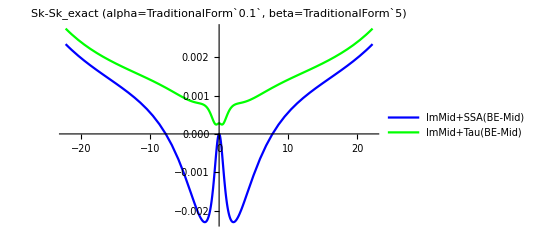

```mathematica
alpha0=0.1;
beta0=5;
Plot[{S5[xi,alpha0,beta0]-S0[xi],S7[xi,alpha0,beta0]-S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotStyle->{Blue,Green},PlotLegends->{"ImMid+SSA(BE-Mid)","ImMid+Tau(BE-Mid)"},PlotLabel->StringForm["Sk-Sk_exact (alpha=``, beta=``)",alpha0,beta0]]
```

```mathematica
beta0=5;
Manipulate[Plot[{S5[xi,alpha,beta0],S7[xi,alpha,beta0],S0[xi]},{xi,-xiMax[alpha,beta0],xiMax[alpha,beta0]},PlotRange->{0.5nbVal,1.25S0[0]},PlotStyle->{Red,Blue,{Black,Dashed}},PlotLegends->{"ImMid+SSA(BE-Mid)","ImMid+Tau(BE-Mid)"}],{alpha,0.01,1}]
```

### Comparison of Explicit Schemes

```mathematica
alpha0=0.05;
Manipulate[Plot[{S9[xi,alpha0,beta],S10[xi,alpha0,beta],S11[xi,alpha0,beta],S12[xi,alpha0,beta],S0[xi]},{xi,-xiMax[alpha0,beta],xiMax[alpha0,beta]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,Green,Purple,Black},PlotLegends->{"ExMid+SSA","ExMid+Tau","MN2+SSA+MN2","SSA2+MN+SSA2","Exact"}],{beta,2alpha0,0.25}]
Manipulate[Plot[{S9[xi,alpha0,beta]-S0[xi],S10[xi,alpha0,beta]-S0[xi],S11[xi,alpha0,beta]-S0[xi],S12[xi,alpha0,beta]-S0[xi]},{xi,-xiMax[alpha0,beta],xiMax[alpha0,beta]},PlotStyle->{Red,Blue,Green,Purple},PlotLegends->{"ExMid+SSA","ExMid+Tau","MN/2+SSA+MN/2","SSA/2+MN+SSA/2"}],{beta,2alpha0,0.25}]
```

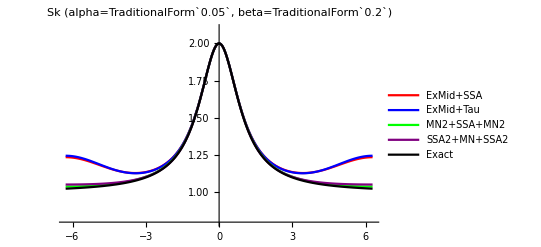

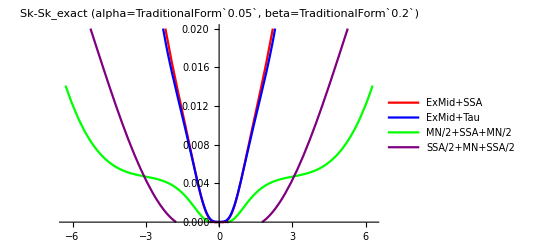

```mathematica
alpha0=0.05;
beta0=0.2;
Plot[{S9[xi,alpha0,beta0],S10[xi,alpha0,beta0],S11[xi,alpha0,beta0],S12[xi,alpha0,beta0],S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,Green,Purple,Black},PlotLegends->{"ExMid+SSA","ExMid+Tau","MN2+SSA+MN2","SSA2+MN+SSA2","Exact"},PlotLabel->StringForm["Sk (alpha=``, beta=``)",alpha0,beta0]]
Plot[{S9[xi,alpha0,beta0]-S0[xi],S10[xi,alpha0,beta0]-S0[xi],S11[xi,alpha0,beta0]-S0[xi],S12[xi,alpha0,beta0]-S0[xi]},{xi,-xiMax[alpha0,beta0],xiMax[alpha0,beta0]},PlotStyle->{Red,Blue,Green,Purple},PlotLegends->{"ExMid+SSA","ExMid+Tau","MN/2+SSA+MN/2","SSA/2+MN+SSA/2"},PlotLabel->StringForm["Sk-Sk_exact (alpha=``, beta=``)",alpha0,beta0],PlotRange->{0,0.02}]
```

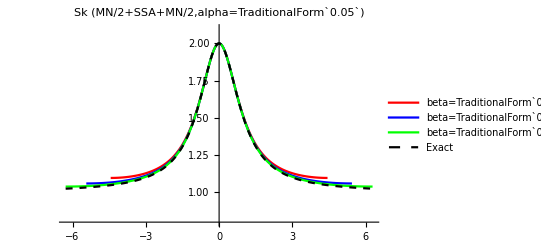

```mathematica
alpha0=0.05;
beta1=0.1;beta2=0.15;beta3=0.2;
Plot[{S11[xi,alpha0,beta1]Boole[Abs[xi]<xiMax[alpha0,beta1]],S11[xi,alpha0,beta2]Boole[Abs[xi]<xiMax[alpha0,beta2]],S11[xi,alpha0,beta3]Boole[Abs[xi]<xiMax[alpha0,beta3]],S0[xi]},{xi,-xiMax[alpha0,beta3],xiMax[alpha0,beta3]},PlotRange->{0.8,2.1},PlotStyle->{Red,Blue,Green,{Black,Dashed}},PlotLegends->{StringForm["beta=``",beta1],StringForm["beta=``",beta2],StringForm["beta=``",beta3],"Exact"},PlotLabel->StringForm["Sk (MN/2+SSA+MN/2,alpha=``)",alpha0]]
```